```mathematica
Needs["GeneralUtilities`"]
```

## Wright Equilibrium functions

In this code and elsewhere, x is frequency of wildtype (in contrast with the main text!!!)
Exp[σ x] is the effect of selection (i.e. s = 2 N_e Δ) s is positive when mutants have a fitness cost (the typical case).

```mathematica
(*Integrate[Exp[σ x](1-x)^(-1+α) x^(-1+β),{x,0,1}]*)
```

ConditionalExpression[Gamma[α] Gamma[β] Hypergeometric1F1Regularized[β,α+β,σ],Re[α]>0&&Re[β]>0]

```mathematica
(*NeutralDist[d_,q_][x_]:=((1-x)^(-1+d (1-q)) x^(-1+d q))/Beta[d q,d (1-q)]*)
```

```mathematica
(*FrequencyMGF[d_,q_][s_]:=(Gamma[d q] Gamma[d-d q] Hypergeometric1F1[d q,d,s])/Gamma[d]*)
```

```mathematica
(*FrequencyDist[d_,q_,s_][x_]:=(Exp[s x](1-x)^(-1+d (1-q)) x^(-1+d q))/(FrequencyMGF[d,q][s])*)
```

```mathematica
(*CountLikelihood[d_,q_,s_][k_,n_]:=-Log[Binomial[n,k]]+LogGamma[d q]+LogGamma[d(1- q)]-LogGamma[d(1- q)+(-k+n)]-LogGamma[k+d q]+ Log[Hypergeometric1F1Regularized[d q,d,s]]-Log[Hypergeometric1F1Regularized[k+d q,d+n,s]]*)
```

α = 2 μN_e = D(1-q) and β=2μ†N_e= Dq. Note that (unfortunately) this makes α and β the opposite order: The neutral distribution is BetaDistribution[β,α].  It’s not quite so bad in the paper, becasue β -> α† .

```mathematica
FrequencyMGF[σ_,{α_,β_}]:=Beta[α,β]Hypergeometric1F1[β,α+β,σ]
```

```mathematica
FrequencyDist[σ_,{α_,β_}][x_]:=(Exp[σ x](1-x)^(-1+α) x^(-1+β))/FrequencyMGF[σ,{α,β}]
```

```mathematica
CountLikelihood[σ_,{α_,β_}][{j_,k_}] := Log[Binomial[j+k,j]]-Log[Hypergeometric1F1Regularized[β,α+β,σ]]+Log[Hypergeometric1F1Regularized[j+β,j+k+α+β,σ]]-LogGamma[α]+LogGamma[k+α]-LogGamma[β]+LogGamma[j+β]
```

```mathematica
MeanFrequency[σ_,{α_,β_}]:=(β Hypergeometric1F1[1+β,1+α+β,σ])/((α+β) Hypergeometric1F1[β,α+β,σ]);
```

If s is too large this sampler becomes time consuming.

```mathematica
RandomWrightSample[σ_,{α_,β_}]:=Module[{limit,k,total},
total=0;
 (*uses inverse CDF sampling to get reweighted sample*)
limit=(Gamma[β] Hypergeometric1F1[β,α+β,σ])/Gamma[α+β] RandomReal[];
k=0;
While[total<limit,
total=total+(σ^k  Gamma[k+β])/(k! Gamma[k+α+β]);
k=k+1;
];
k=k-1;(*Return the previous thing*)
RandomVariate[BetaDistribution[β+k, α]]
]
```

You can check that the Gibbs Sampling algorithm works properly

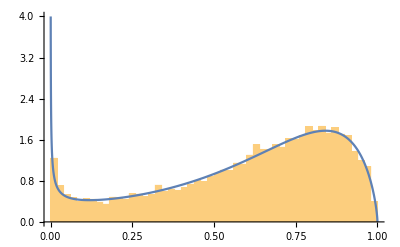

```mathematica
(*
Show[Histogram[Table[RandomWrightSample[5,{1.7,0.5}],10000],{0,1,.02},"PDF"],Plot[FrequencyDist[5,{1.7,0.5}][x],{x,0,1},PlotRange->{0,4}]]*)
```

## Codon analysis

```mathematica
codonRules=Module[{aaCodon,ruleMaker},aaCodon={{"A",{"GCT","GCC","GCA","GCG"}},{"R",{"CGT","CGC","CGA","CGG","AGA","AGG"}},{"N",{"AAT","AAC"}},{"D",{"GAT","GAC"}},{"C",{"TGT","TGC"}},{"Q",{"CAA","CAG"}},{"E",{"GAA","GAG"}},{"G",{"GGT","GGC","GGA","GGG"}},{"H",{"CAT","CAC"}},{"I",{"ATT","ATC","ATA"}},{"L",{"TTA","TTG","CTT","CTC","CTA","CTG"}},{"K",{"AAA","AAG"}},{"M",{"ATG"}},{"F",{"TTT","TTC"}},{"P",{"CCT","CCC","CCA","CCG"}},{"S",{"TCT","TCC","TCA","TCG","AGT","AGC"}},{"T",{"ACT","ACC","ACA","ACG"}},{"W",{"TGG"}},{"Y",{"TAT","TAC"}},{"V",{"GTT","GTC","GTA","GTG"}},{"*",{"TAA","TGA","TAG"}}};
ruleMaker[amine_,list_]:=(#->amine)&/@list;
Flatten[Apply[ruleMaker,Map[Characters,aaCodon,{3}],{1}]]];
allCodons=First/@codonRules;
allAAs=DeleteDuplicates[Last/@codonRules];
ntRules={"A"->1,"C"->2,"G"->3,"T"->4,"-"->5,"N"->6};
aaCodon=Rule@@MapAt[Characters,#,2]&/@{{"A",{"GCT","GCC","GCA","GCG"}},{"R",{"CGT","CGC","CGA","CGG","AGA","AGG"}},{"N",{"AAT","AAC"}},{"D",{"GAT","GAC"}},{"C",{"TGT","TGC"}},{"Q",{"CAA","CAG"}},{"E",{"GAA","GAG"}},{"G",{"GGT","GGC","GGA","GGG"}},{"H",{"CAT","CAC"}},{"I",{"ATT","ATC","ATA"}},{"L",{"TTA","TTG","CTT","CTC","CTA","CTG"}},{"K",{"AAA","AAG"}},{"M",{"ATG"}},{"F",{"TTT","TTC"}},{"P",{"CCT","CCC","CCA","CCG"}},{"S",{"TCT","TCC","TCA","TCG","AGT","AGC"}},{"T",{"ACT","ACC","ACA","ACG"}},{"W",{"TGG"}},{"Y",{"TAT","TAC"}},{"V",{"GTT","GTC","GTA","GTG"}},{"*",{"TAA","TGA","TAG"}}};
```

```mathematica
val=Plus@@((# 4^{2,1,0})/64.)&/@ (*This digit ordering seems to best separate the aa's and also seems to match the grouping on Wikipedia.*)((Part[#,{2,1,3}]&/@allCodons)/.{"T"->0,"A"->3,"C"->1,"G"->2});
aminoVal=Rule@@@Transpose[{allAAs,
ReplacePart[(Mean@Part[#,2]&/@Transpose/@GatherBy[Transpose[{allCodons,val}]/.codonRules,First]),-1->1.0]}];
```

```mathematica
AAs=SortBy[allAAs,(#/.aminoVal)&];
```

```mathematica
binaryAminos=Block[{aaCodon={{"A",{"GCT","GCC","GCA","GCG"}},{"R",{"CGT","CGC","CGA","CGG","AGA","AGG"}},{"N",{"AAT","AAC"}},{"D",{"GAT","GAC"}},{"C",{"TGT","TGC"}},{"Q",{"CAA","CAG"}},{"E",{"GAA","GAG"}},{"G",{"GGT","GGC","GGA","GGG"}},{"H",{"CAT","CAC"}},{"I",{"ATT","ATC","ATA"}},{"L",{"TTA","TTG","CTT","CTC","CTA","CTG"}},{"K",{"AAA","AAG"}},{"M",{"ATG"}},{"F",{"TTT","TTC"}},{"P",{"CCT","CCC","CCA","CCG"}},{"S",{"TCT","TCC","TCA","TCG","AGT","AGC"}},{"T",{"ACT","ACC","ACA","ACG"}},{"W",{"TGG"}},{"Y",{"TAT","TAC"}},{"V",{"GTT","GTC","GTA","GTG"}},{"*",{"TAA","TGA","TAG"}}},mat,b},
Table[b=Characters/@gg[[2]];
Rule[gg[[1]],Boole[Length[b]==2]]
,
{gg,aaCodon}]
];
```

```mathematica
fourfoldAminos=Block[{aaCodon={{"A",{"GCT","GCC","GCA","GCG"}},{"R",{"CGT","CGC","CGA","CGG","AGA","AGG"}},{"N",{"AAT","AAC"}},{"D",{"GAT","GAC"}},{"C",{"TGT","TGC"}},{"Q",{"CAA","CAG"}},{"E",{"GAA","GAG"}},{"G",{"GGT","GGC","GGA","GGG"}},{"H",{"CAT","CAC"}},{"I",{"ATT","ATC","ATA"}},{"L",{"TTA","TTG","CTT","CTC","CTA","CTG"}},{"K",{"AAA","AAG"}},{"M",{"ATG"}},{"F",{"TTT","TTC"}},{"P",{"CCT","CCC","CCA","CCG"}},{"S",{"TCT","TCC","TCA","TCG","AGT","AGC"}},{"T",{"ACT","ACC","ACA","ACG"}},{"W",{"TGG"}},{"Y",{"TAT","TAC"}},{"V",{"GTT","GTC","GTA","GTG"}},{"*",{"TAA","TGA","TAG"}}},mat,b},
Table[b=Characters/@gg[[2]];
Rule[gg[[1]],Boole[Length[b]==4]]
,
{gg,aaCodon}]
];
```

```mathematica
SequenceOverlap[seq1_,seq2_]:=Total[MapThread[Boole[#1==#2]&,{seq1,seq2}]]
```

```mathematica
SequenceDifference[l1_,l2_]:=Select[MapThread[Rule,{l1,l2}],(Part[#,1]≠ Part[#,2])&]
```

```mathematica
SNPCodonFrequency[snpmatrix_,codon_]:=
(*Takes a length-3 list of snps and codon. Returns frequency of codon under indepence of mutations assumption.*)
Block[{ind,normsnp},
ind=codon/.ntRules;
normsnp=Table[N[(snp/Max[Total[snp],1])],{snp,snpmatrix}];
Times@@Table[normsnp[[ii,ind[[ii]] ]],{ii,1,3}]]
```

```mathematica
SNPAAfreq[patient_,day_,amine_]:=Table[Total[SNPCodonFrequency[SNPPatientDay[patient,day][amine],#]&/@(aminoAcid/.aaCodon)]
,{aminoAcid,AAs}];
```

```mathematica
SNPAArule[patient_,day_,amine_]:=
(*really useful function. Returns a list of rules from amino acids to frequency values*)
Table[aminoAcid->Total[SNPCodonFrequency[SNPPatientDay[patient,day][amine],#]&/@(aminoAcid/.aaCodon)]
,{aminoAcid,AAs}];
```

```mathematica
SNPAAfreqList[patient_,day_,loc_][AAs_]:=Table[Total[SNPCodonFrequency[SNPPatientDay[patient,day][loc],#]&/@(aminoAcid/.aaCodon)]
,{aminoAcid,AAs}];
```

```mathematica
SNPBinarFreq[patient_,day_,amine_]:=Total[Table[(aminoAcid/.binaryAminos)*Total[SNPCodonFrequency[SNPPatientDay[patient,day][amine],#]&/@(aminoAcid/.aaCodon)]^2
,{aminoAcid,AAs}]];
```

```mathematica
SNPFourfoldFreq[patient_,day_,amine_]:=Total[Table[(aminoAcid/.fourfoldAminos)*Total[SNPCodonFrequency[SNPPatientDay[patient,day][amine],#]&/@(aminoAcid/.aaCodon)]^2
,{aminoAcid,AAs}]];
```

```mathematica
TransitionsTransversions[rule_]:=With[
{types={"G"->"pur","A"->"pur","T"->"pyr","C"->"pyr"}},
If[Length[rule]==1,
{Total[Boole/@Equal@@@(rule/.types)],
Total[Boole/@Unequal@@@(rule/.types)]},{0,0}]]
```

```mathematica
MeanTransistionsTransversions[InCodons_,OutCodons_]:=Mean[
Table[
Total[Table[TransitionsTransversions[SequenceDifference[in,out]],{out,OutCodons}]],{in,InCodons}]]
```

```mathematica
{"G"->"C"}/.{"G"->"pur","A"->"pur","T"->"pyr","C"->"pyr"}
```

{pur→pyr}

```mathematica
NearbyCodon[codon_,codonlist_]:=Or@@((SequenceOverlap[codon,#]==2)&/@codonlist)
```

```mathematica
μνRates[transversionRatio_][startsites_,endsites_]:=Module[{InCodons,OutCodons},
(*This is the forward and backward mutation rate measured with respect to the tranversion rate. 2N_e {μ,ν} gives the forward and backward α's *)
InCodons=Join@@(startsites/.aaCodon);
OutCodons=Join@@(endsites/.aaCodon);
OutCodons=Select[OutCodons,NearbyCodon[#1,InCodons]&];
With[{
v =Normalize[{transversionRatio,1}],
q = MeanTransistionsTransversions[InCodons,OutCodons],
p=MeanTransistionsTransversions[OutCodons,InCodons]},
Flatten[{{{q}, {p}}}.{1,1/(transversionRatio)}]]
](*returns function of (αts0, αtv0) that returns {αts, α, β} *)
```

## Effective Population Size

```mathematica
UpdateS[data_][s_]:=Block[{dat,ns,mk,f1,f2,a,c},
dat=Select[data,(Length[#]==2&&Total[#]>2)&];
If[Length[dat]<2,
Return[0.0],
mk={0.5,0.5};
ns=Total/@dat;
f1=Total[PolyGamma[s]-PolyGamma[ns+s]+((PolyGamma[(#+s mk)]-PolyGamma[s mk])&/@dat).mk];
f2=Total[PolyGamma[1,s]-PolyGamma[1,ns+s]+((PolyGamma[1,(#+s mk)]-PolyGamma[1,s mk])&/@dat).mk^2];
a=-s^2 f2;
c=f1-a/s;
If[c≥0,
a=s^3(s f2 + 2 f1);
c=-(s^2 f1+a/s);
];
Return[-a/c];]
]
```

```mathematica
FindS[data_]:=FixedPoint[UpdateS[data],0.01,SameTest->(Abs[#1-#2]<1*^-8&)]
```

```mathematica
FindNeutralθ[data_]:=1/2 FindS[data]
```

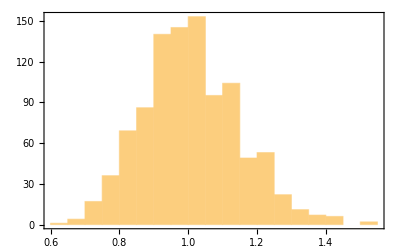

```mathematica
(*With[{θ=.2,n=100,nn=100},Histogram[1/θ*Table[FindNeutralθ[{#,n-#}&/@RandomVariate[BetaBinomialDistribution[θ,θ,n],nn]],1000],20]]*)
```

## Fisher Exact Test

Maybe this will be useful someday

```mathematica
RandMargPerm[ntmarg_,daymarg_]:=Block[{n,mat,ntlist,row},
ntlist=ntmarg;
Table[
If[marg>0,
row=RandomVariate[MultivariateHypergeometricDistribution[marg,ntlist]];
,
row =ntlist*0;
];
ntlist-=row;
row
,{marg,daymarg}]
]
```

```mathematica
Margins[mat_]:={Total/@Transpose@mat,Total/@mat};(*{colTotals, rowtotals}*)
logfac[n_]:=LogGamma[n+1.0]
```

## Rebound dynamics

```mathematica
GetK[data_]:=Mean[(N[√(#[[2]])])&/@Select[data,(And[#[[1]]<2,#[[1]]≥-1])&]]^2
```

```mathematica
NonRespondQ[series_]:=Module[{startval,dip},
startval=Sqrt@GetK[series];
dip=Mean[Sqrt@Select[series,(10>#[[1]]>3)&][[;;,2]]];
(dip-startval)/startval>-0.05];
Dip[series_]:=Module[{max,min},
{min,max}=Quantile[Sqrt@Select[series,(56≥#[[1]]≥0)&][[;;,2]],{.2,.8}];
Log[#/(1-#)]&[( Max[max,5]-Max[min,5])/Max[max,5]]
];
```

```mathematica
Solve[LogisticSigmoid[x]==y,x]
```

{{x→ConditionalExpression[2 ⅈ π C[1]+Log[-y/(-1+y)],C[1]∈ℤ]}}

```mathematica
reboundDynamics[λ_,λ2_,x_,k_][t_]:=
(*growthrate, decay rate, start frequency of resisters, k*)
-(ⅇ^(-t λ2))^HeavisideTheta[t] k (-1+x)+k x (1/(-ⅇ^(-t λ) (-1+x)+x))^HeavisideTheta[t]
```

```mathematica
reboundDynamicsError[λ_,λ2_,x_,k_][{t_,c_}]:=
(*growth, decay, initfraction, capacity*)
If[-2≤t<60,
(If[c>20,
Norm[Sqrt[-(ⅇ^(-t λ2))^HeavisideTheta[t] k (-1+x)+k x (1/(-ⅇ^(-t λ) (-1+x)+x))^HeavisideTheta[t]]-Sqrt[c]]^2,
If[-(ⅇ^(-t λ2))^HeavisideTheta[t] k (-1+x)+k x (1/(-ⅇ^(-t λ) (-1+x)+x))^HeavisideTheta[t]<20,
0,
Norm[Sqrt[-(ⅇ^(-t λ2))^HeavisideTheta[t] k (-1+x)+k x (1/(-ⅇ^(-t λ) (-1+x)+x))^HeavisideTheta[t]]-Sqrt[20]]^2]/.t->t-1
]),0]
```

```mathematica
Fitλandλ2andXassociation[datas_]:=Module[{te,init,symb,flatsymb,xvarchange,initvals,krules,xrules,conditions,newa,unknowns,jumpvals,minvals,maxvals},
krules=MapThread[Rule,
{Table[Symbol["n"<>ToString[ii]],{ii,Keys[datas]}]
,Values[GetK/@datas]}];
xrules=Join[Table[If[NonRespondQ[datas[[ii]]],
Symbol["x"<>ToString[ii]]->1,Nothing],{ii,Keys[datas]}],
Table[If[ii=="2C2",
Symbol["x"<>ToString[ii]]->10^-15.,Nothing],{ii,Keys[datas]}]
];
conditions = Join[krules,xrules,{λ1->1/3.}]; 
xvarchange=Table[
Symbol["x"<>ToString[ii]]->LogisticSigmoid[Symbol["x"<>ToString[ii]]],{ii,Keys[datas]}];
symb={λ1,λ2,Table[{Symbol["x"<>ToString[ii]],Symbol["n"<>ToString[ii]]},{ii,Keys[datas]}]};
flatsymb=Select[Flatten[symb/.conditions],(Not[NumberQ[N[#]]])&];
unknowns=StringDrop[ToString[#],1]&/@Drop[flatsymb,{1}];
minvals=Flatten[{.1,
Table[-5,{key,unknowns}]}];
maxvals=Flatten[{.8,
Table[0,{key,unknowns}]}];
te=TotalErrors[Sequence@@(Evaluate[symb/.conditions]/.xvarchange),Values[datas]];init=MapThread[List,{flatsymb,minvals,maxvals}];
newa=Association[
Join[
{"decay"->λ2,"growth"->λ1},
{"patients"-><|
Table[key-><|<| "trace"->datas[key]|>,
<|"x"->Symbol["x"<>key]|>,
<|"k"->Symbol["n"<>key]|>|>,
{key,Keys[datas]}]|>
}
]];
(Evaluate[newa/.conditions]/.xvarchange)/.
NMinimize[te,init,Method->"DifferentialEvolution"(*,AccuracyGoal->20,MaxIterations->200,Method->"PrincipalAxis"*)][[2]]
(*FindMinimum[te,init,AccuracyGoal->20,Method->"PrincipalAxis"]*)
]
```

```mathematica
TotalErrors[λ_,λ2_,xkmat_,datas_ ]:=Mean[MapThread[
Total[reboundDynamicsError[λ,λ2,Sequence@@#2]/@#1]&,
{datas,xkmat}]]
```

## Extra Code

```mathematica
(*Fitλandλ2andXassociation[datas_]:=Module[{te,init,symb,flatsymb,xvarchange,initvals,krules,xrules,conditions,newa,unknowns,jumpvals,minvals,maxvals},
krules=MapThread[Rule,
{Table[Symbol["n"<>ToString[ii]],{ii,Keys[datas]}]
,Values[GetK/@datas]}];
xrules=Table[If[NonRespondQ[datas[[ii]]],
Symbol["x"<>ToString[ii]]->1,Nothing],{ii,Keys[datas]}];
conditions = Join[krules,xrules,{λ1->1/3.}]; 
xvarchange=Table[
Symbol["x"<>ToString[ii]]->LogisticSigmoid[Symbol["x"<>ToString[ii]]],{ii,Keys[datas]}];
symb={λ1,λ2,Table[{Symbol["x"<>ToString[ii]],Symbol["n"<>ToString[ii]]},{ii,Keys[datas]}]};
flatsymb=Select[Flatten[symb/.conditions],(Not[NumberQ[N[#]]])&];
unknowns=StringDrop[ToString[#],1]&/@Drop[flatsymb,{1}];
minvals=Flatten[{.1,
Table[-5,{key,unknowns}]}];
maxvals=Flatten[{.8,
Table[0,{key,unknowns}]}];
te=TotalErrors[Sequence@@(Evaluate[symb/.conditions]/.xvarchange),Values[datas]];init=MapThread[List,{flatsymb,minvals,maxvals}];
newa=Association[
Join[
{"decay"->λ2,"growth"->λ1},
{"patients"-><|
Table[key-><|<| "trace"->datas[key]|>,
<|"x"->Symbol["x"<>key]|>,
<|"k"->Symbol["n"<>key]|>|>,
{key,Keys[datas]}]|>
}
]];
(Evaluate[newa/.conditions]/.xvarchange)/.
NMinimize[te,init,Method->"DifferentialEvolution"(*,AccuracyGoal->20,MaxIterations->200,Method->"PrincipalAxis"*)][[2]]
(*FindMinimum[te,init,AccuracyGoal->20,Method->"PrincipalAxis"]*)
];*)
```

```mathematica
(*Fitλandλ2andX[datas_]:=Module[{te,init,symb,flatsymb,xvarchange,initvals,krules,xrules,conditions},
krules=MapThread[Rule,
{Table[Symbol["n"<>ToString[ii]],{ii,Length[datas]}]
,GetK/@datas}];
xrules=Table[If[NonRespondQ[datas[[ii]]],
Symbol["x"<>ToString[ii]]->1,Nothing],{ii,Length[datas]}];
conditions = Join[krules,xrules,{λ1->1/3.}];
xvarchange=Table[
Symbol["x"<>ToString[ii]]->LogisticSigmoid[Symbol["x"<>ToString[ii]]],{ii,Length[datas]}];
symb={λ1,λ2,Table[{Symbol["x"<>ToString[ii]],Symbol["n"<>ToString[ii]]},{ii,1,Length[datas]}]};
flatsymb=Select[Flatten[symb/.conditions],(Not[NumberQ[#]])&];
initvals=Flatten[{.5,Table[-2,{ii,Length[flatsymb]-1}]}];
te=TotalErrors[Sequence@@(Evaluate[symb/.conditions]/.xvarchange),datas];init=MapThread[List,{flatsymb,initvals}];
(Evaluate[symb/.conditions]/.xvarchange)/.
FindMinimum[te,init,AccuracyGoal->20,MaxIterations->200,Method->"PrincipalAxis"][[2]]
(*FindMinimum[te,init,AccuracyGoal->20,Method->"PrincipalAxis"]*)
];*)
```

```mathematica
(*FitXandK[data_,λ_,λ2_]:=Module[{likelihood,times,mincounts,maxcounts,output,x,k},
likelihood=Function[{x,k},Total[reboundDynamicsError[λ,λ2,x,k]/@data]];
maxcounts=Max[data[[;;,2]]];
mincounts=Max[Min[data[[;;,2]]],10];
If[NonRespondQ[data],
output={1,Exp[k]}/.FindMinimum[likelihood[1,Exp[k]],{k,Log[maxcounts]}][[2]];
,
output={Exp[-Log[1+Exp[x]]],Exp[k]}/.FindMinimum[likelihood[Exp[-Log[1+Exp[x]]],Exp[k]],{x,-Log[0.5 mincounts/maxcounts]},{k,Log[maxcounts]},Method->"PrincipalAxis"][[2]];];
Return[output];
]*)
```

```mathematica
(*Fitλandλ2[datas_,xkmat_]:=Module[{likelihood,times,counts,output,λ,λ2},
likelihood=Function[{λ,λ2},
Mean[MapThread[
Total[Boole[Not[NonRespondQ[#1]]]*reboundDynamicsError[λ,λ2,Sequence@@#2]/@#1]&,
{datas,xkmat}]]];
output={Exp[λ],Exp[λ2]}/.FindMinimum[likelihood[Exp[λ],Exp[λ2]],{λ,0},{λ2,0},Method->"PrincipalAxis"][[2]];
Return[output];
]*)
```

```mathematica
(**)
```

```mathematica
(*FitDatas[datas_,λstart_,λ2start_]:=
Module[{likelihood,xkmat,λ1,λ2,error,newerror},
error=10^8.;
newerror=10^7;
{λ1,λ2} = {λstart,λ2start};
While[Abs[error-newerror]>1,
xkmat=Table[FitXandK[data,λ1,λ2],{data,datas}];
{λ1,λ2}=Fitλandλ2[datas,xkmat];
error =newerror;
newerror = TotalErrors[λ1,λ2,xkmat,datas]];
Return[{λ1,λ2,xkmat}]
]*)
```

```mathematica
(*errorR[r_?NumericQ][key_,data_]:=Module[{out},
If[key=="2C2",(*override for putting in patients "by hand"*)
{Total[reboundDynamicsError[1/3,r,10^-20.,GetK[data]]/@data],10^-20.},
 If[NonRespondQ[data],{0,1},
out=NMinimize[{Total[reboundDynamicsError[1/3,r,LogisticSigmoid[x],GetK[data]]/@data],-27<x<3.},{x},Method->"DifferentialEvolution"];
{out[[1]],LogisticSigmoid[x]/.out[[2]]}
]
]]*)
```

```mathematica
(*errorRfun[r_][datas_]:=Total[KeyValueMap[Function[{key,value},errorR[r][key,value][[1]]],datas]]
RInterp[datas_]:=Module[{f},
f=Interpolation[Table[{r,errorRfun[r][datas]},{r,.1,.4,.02}]];
Return[f]
]
GetR[datas_]:=Module[{f},
f=RInterp[datas];
x/.NMinimize[{outt[x],.1<x<.4},{x}][[2,1]]
]
Fitλandλ2andXassociation[datas_]:=Module[{r},
r =GetR[datas];
Association["decay"->r,"growth"->1/3.,"patients"->
Association[KeyValueMap[
Function[{key,value},
Association[key->Association[
"trace"->value,
"x"->errorR[r][key,value][[2]],
"k"->GetK[value]
]]],
datas]]
]
]*)
```